Defining the function here first.

```mathematica
p[N_,V_,T_]:=N *k* T* Exp[-a* N /(k T V)]/(V-b *N)
```

First derivative check:

```mathematica
Simplify[D[p[N,V,T],V]]
```

-(ⅇ^(-(a N)/(k T V)) N (a N (b N-V)+k T V^2))/(V^2 (-b N+V)^2)

Second derivative check:

```mathematica
D[p[N,V,T],{V,2}]
```

```mathematica
(2 ⅇ^(-(a N)/(k T V)) k N T)/(-b N+V)^3-(2 a ⅇ^(-(a N)/(k T V)) N^2)/(V^2 (-b N+V)^2)+(k N T ((a^2 ⅇ^(-(a N)/(k T V)) N^2)/(k^2 T^2 V^4)-(2 a ⅇ^(-(a N)/(k T V)) N)/(k T V^3)))/(-b N+V)
```

(2 ⅇ^(-(a N)/(k T V)) k N T)/(-b N+V)^3-(2 a ⅇ^(-(a N)/(k T V)) N^2)/(V^2 (-b N+V)^2)+(k N T ((a^2 ⅇ^(-(a N)/(k T V)) N^2)/(k^2 T^2 V^4)-(2 a ⅇ^(-(a N)/(k T V)) N)/(k T V^3)))/(-b N+V)

```mathematica
Expand[%]
```

-(2 ⅇ^(-(a N)/(k T V)) k N T)/(b N-V)^3-(a^2 b^2 ⅇ^(-(a N)/(k T V)) N^5)/(k T (b N-V)^3 V^4)+(2 a b^2 ⅇ^(-(a N)/(k T V)) N^4)/((b N-V)^3 V^3)+(2 a^2 b ⅇ^(-(a N)/(k T V)) N^4)/(k T (b N-V)^3 V^3)-(6 a b ⅇ^(-(a N)/(k T V)) N^3)/((b N-V)^3 V^2)-(a^2 ⅇ^(-(a N)/(k T V)) N^3)/(k T (b N-V)^3 V^2)+(4 a ⅇ^(-(a N)/(k T V)) N^2)/((b N-V)^3 V)

```mathematica
Simplify[%]
```

-(ⅇ^(-(a N)/(k T V)) N (2 k^2 T^2 V^4+a^2 N^2 (-b N+V)^2-2 a k N T V (b^2 N^2-3 b N V+2 V^2)))/(k T (b N-V)^3 V^4)

```mathematica
s = Solve[D[p[N, V, T], V] == 0 && D[D[p[N, V, T], V], V] == 0, {V, T}, Reals]
```

{{V→2 b N,T→a/(4 b k)}}

```mathematica
p[N,V,T]/.s[[1]]
```

a/(4 b^2 ⅇ^2)

Plotting number 7

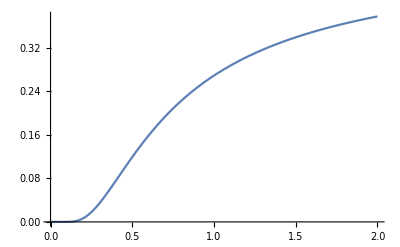

```mathematica
Plot[1/(1+Exp[1/x]),{x,0,2}]
```